```mathematica
(* Model from Ma et al 2023 - a slight change from Hall 2004 *)
Clear[wbar,xf,xm,y,so,ssry,ssr,ssro,dY,dO,t,tms,h];
wbarxf=xf xm+(1-h ssr) (xm (1-xf)+xf (1-xm))+(1-ssr)(1-xf) (1-xm);
wbarxm=1/2 xf y+1/2 (1-so) xf (1-y)+(1/2+dY) y (1-xf) (1-ssry)+(1/2+dO) (1-ssro) (1-y) (1-xf);
wbary=1/2 xf y+1/2 (1-so) xf (1-y)+(1/2-dY) y (1-xf) (1-ssry)+(1/2-dO) (1-ssro) (1-y) (1-xf);

xfnext=FullSimplify[(xf xm+1/2 (1-h ssr) (xm (1-xf)+xf (1-xm)))/wbarxf]
xmnext=FullSimplify[(1/2 xf y+1/2 (1-so) xf (1-y))/wbarxm]
ynext=FullSimplify[(1/2 xf y+(1/2-dY) y (1-xf)(1-ssry))/wbary]
```

(xf+xm-h ssr xm+h ssr xf (-1+2 xm))/(2+2 ssr (-1+xf+xm-h xm-xf xm+h xf (-1+2 xm)))

(xf+so xf (-1+y))/(1-ssro+ssro xf-2 dO (-1+ssro) (-1+xf) (-1+y)+so xf (-1+y)+(-ssro+2 dY (-1+ssry)+ssry) (-1+xf) y)

((-1+ssry+2 dY (-1+ssry) (-1+xf)-ssry xf) y)/(-1+ssro-ssro xf-2 dO (-1+ssro) (-1+xf) (-1+y)+(ssro+2 dY (-1+ssry)-ssry) (-1+xf) y+so (xf-xf y))

```mathematica
(* Equilibrium of Driver alone *)
y=1;h=0;
XfreqAlone=FullSimplify[Solve[{xfnext==xf,xmnext==xm},{xf,xm}]]
(* no cost in males *)
ssry=0; XfreqAloneNMC=FullSimplify[Solve[{xfnext==xf,xmnext==xm},{xf,xm}]]
Clear[ssry]
(* no cost in females *)
ssr=0;XfreqAloneNFC=FullSimplify[Solve[{xfnext==xf,xmnext==xm},{xf,xm}]]
Clear[ssr]
```

{{xf→0,xm→0},{xf→1,xm→1},{xf→1-1/(2 ssr)+1/(2 ssr+4 dY ssr-2 ssr ssry-4 dY ssr ssry),xm→-(2 ssr (-1+ssry)+2 dY (-1+2 ssr) (-1+ssry)-ssry)/(2 ssr+(2 dY (-1+ssry)+ssry) (-2 ssr+2 dY (-1+ssry)+ssry))}}

{{xf→0,xm→0},{xf→1,xm→1},{xf→1-dY/(ssr+2 dY ssr),xm→(ssr+dY (-1+2 ssr))/(ssr+2 dY (dY+ssr))}}

{{xf→0,xm→0},{xf→1,xm→1}}

(* Attempt to simplify with dY=1/2*)

dY=1/2; FullSimplify[XfreqAloneNMC]
FullSimplify[XfreqAloneNFC]
FullSimplify[XfreqAlone]

{{xf→0,xm→0},{xf→1,xm→1},{xf→1-1/(4 ssr),xm→1-2/(1+4 ssr)}}

{{xf→0,xm→0},{xf→1,xm→1}}

{{xf→0,xm→0},{xf→1,xm→1},{xf→1-1/(2 ssr)+1/(4 ssr-4 ssr ssry),xm→(-1-4 ssr (-1+ssry)+2 ssry)/((1-2 ssry)^2-4 ssr (-1+ssry))}}

```mathematica
Clear[ssry,ssr,h]
Xfemale=FullSimplify[1-(1-1/(2 ssr)+1/(2 ssr+4 dY ssr-2 ssr ssry-4 dY ssr ssry))]
Xmale=FullSimplify[1-(-(2 ssr (-1+ssry)+2 dY (-1+2 ssr) (-1+ssry)-ssry)/(2 ssr+(2 dY (-1+ssry)+ssry) (-2 ssr+2 dY (-1+ssry)+ssry)))]
Clear[xf];h=0.135; ssr=0.59; ssry=0;XfreqAlone
Plot[{1-(1-1/(2 ssr)+1/(2 ssr+4 dY ssr-2 ssr ssry-4 dY ssr ssry)),1+(2 ssr (-1+ssry)+2 dY (-1+2 ssr) (-1+ssry)-ssry)/(2 ssr+(2 dY (-1+ssry)+ssry) (-2 ssr+2 dY (-1+ssry)+ssry)),0.3},{ssry,0,0.4},PlotRange->{{0,.4},{0,1}},PlotStyle->{Blue,Red,Dashed}]

(*This is figure A.3*)
Plot[{(1-2 ssry)/(4 ssr-4 ssr ssry),(2-6 ssry+4 ssry^2)/((1-2 ssry)^2-4 ssr (-1+ssry))},{ssry,0,0.4},PlotRange->{{0,.4},{0,1}},PlotStyle->{Blue,Red,Dashed}]
```

(1-2 ssry)/(4 ssr-4 ssr ssry)

(2-6 ssry+4 ssry^2)/((1-2 ssry)^2-4 ssr (-1+ssry))

{{xf→0,xm→0},{xf→1,xm→1},{xf→0.576271,xm→0.404762}}

-Graphics-

-Graphics-

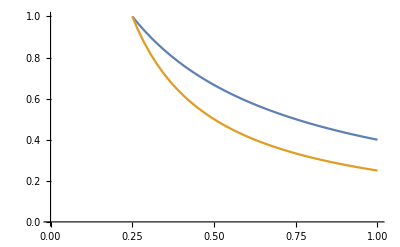

```mathematica
Plot[{2/(1+4 ssr),1/(4ssr)},{ssr,0,1},PlotRange->{{0,1},{0,1}}]
(* So female cost alone can't get us to 15-30% *)
```

```mathematica
Clear[wbar,xf,xm,y,so,ssry,ssr,ssro,dY,dO,t,tms,h];
wbarxf=xf xm+(1-h ssr) (xm (1-xf)+xf (1-xm))+(1-ssr)(1-xf) (1-xm);
wbarxm=1/2 xf y+1/2 (1-so) xf (1-y)+(1/2+dY) y (1-xf) (1-ssry)+(1/2+dO) (1-ssro) (1-y) (1-xf);
wbary=1/2 xf y+1/2 (1-so) xf (1-y)+(1/2-dY) y (1-xf) (1-ssry)+(1/2-dO) (1-ssro) (1-y) (1-xf);

xfnext=FullSimplify[(xf xm+1/2 (1-h ssr) (xm (1-xf)+xf (1-xm)))/wbarxf]
xmnext=FullSimplify[(1/2 xf y+1/2 (1-so) xf (1-y))/wbarxm]
ynext=FullSimplify[(1/2 xf y+(1/2-dY) y (1-xf)(1-ssry))/wbary]
```

(xf+xm-h ssr xm+h ssr xf (-1+2 xm))/(2+2 ssr (-1+xf+xm-h xm-xf xm+h xf (-1+2 xm)))

(xf+so xf (-1+y))/(1-ssro+ssro xf-2 dO (-1+ssro) (-1+xf) (-1+y)+so xf (-1+y)+(-ssro+2 dY (-1+ssry)+ssry) (-1+xf) y)

((-1+ssry+2 dY (-1+ssry) (-1+xf)-ssry xf) y)/(-1+ssro-ssro xf-2 dO (-1+ssro) (-1+xf) (-1+y)+(ssro+2 dY (-1+ssry)-ssry) (-1+xf) y+so (xf-xf y))

```mathematica
h=0;ssro=1-(1-ssry)(1-so);dY=1/2;
FullSimplify[Solve[{xfnext==xf,xmnext==xm,ynext==y},{xf,xm,y}]]
```

{{xf→0,xm→0,y→0},{xf→1,xm→1,y→0},{xf→1,xm→1,y→1},{xf→(1+4 ssr (-1+ssry)-2 ssry)/(4 ssr (-1+ssry)),xm→(-1-4 ssr (-1+ssry)+2 ssry)/((1-2 ssry)^2-4 ssr (-1+ssry)),y→1},{xf→1-1/(2 ssr)+1/(2 ssr+4 dO ssr-2 ssr ssry-4 dO ssr ssry),xm→-(2 ssr (-1+ssry)+2 dO (-1+2 ssr) (-1+ssry)-ssry)/(2 ssr+(2 dO (-1+ssry)+ssry) (-2 ssr+2 dO (-1+ssry)+ssry)),y→0},{xf→1+so/(-1+2 dO (-1+so) (-1+ssry)+ssry-so ssry),xm→((-1+2 dO) (-1+so) (-1+ssry) (-1+2 so ssr+2 dO (-1+so) (-1+ssry)+ssry-so ssry))/(2 so (ssr-ssry) (-1+ssry)+(-1+ssry)^2+4 dO^2 (-1+so)^2 (-1+ssry)^2+4 dO (-1+so) (-1+ssry) (-1+so (ssr-ssry)+ssry)+so^2 (2 ssr-2 ssr ssry+ssry^2)),y→((-1+so) (2 so ssr (-1+ssry)+2 dO (-1+2 so ssr) (-1+ssry)+4 dO^2 (-1+so) (-1+ssry)^2+(-1+ssry) ssry-so ssry^2))/(1+4 dO^2 (-1+so)^2 (-1+ssry)^2-2 ssry+4 dO (-1+so) (-1+ssry) (-1+so ssr+ssry)+(1+so) (2 so ssr (-1+ssry)+ssry^2-so ssry^2))}}

```mathematica
temp=FullSimplify[Solve[{xfnext==xf,xmnext==xm,ynext==y},{xf,xm,y}]][[6]][[3]]
ysupeq=FullSimplify[1-y/.temp]
```

y→((-1+so) (2 so ssr (-1+ssry)+2 dO (-1+2 so ssr) (-1+ssry)+4 dO^2 (-1+so) (-1+ssry)^2+(-1+ssry) ssry-so ssry^2))/(1+4 dO^2 (-1+so)^2 (-1+ssry)^2-2 ssry+4 dO (-1+so) (-1+ssry) (-1+so ssr+ssry)+(1+so) (2 so ssr (-1+ssry)+ssry^2-so ssry^2))

(1-4 so ssr+(-3+so+4 so ssr) ssry-2 (-1+so) ssry^2+2 dO (-1+so) (-1+ssry) (-1+2 ssry))/(1+4 dO^2 (-1+so)^2 (-1+ssry)^2-2 ssry+4 dO (-1+so) (-1+ssry) (-1+so ssr+ssry)+(1+so) (2 so ssr (-1+ssry)+ssry^2-so ssry^2))

(*This is figure A.2*)

ContourPlot[ssup,{ssup,0,1},{dsup,0,0.5},PlotLegends→True,PlotRange→{{0,1},{0,1/2},{0,1}},ContourLabels→All]

-Graphics-